```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={1.04,2.7,3.4};
ωrl={0.6,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
dt=0.01;
t=0.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
ψt=Conjugate[Transpose[Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0]]].ψt;
ψct=X1.ψ000;
ψct=Conjugate[Transpose[Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0]]].ψct;
ψct=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0]]].ψct;
For[ti=dt,ti≤t,ti+=dt,
ψt=Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti].ψt;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti].ψct;
ψcot=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti].ψcot;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];
];
```

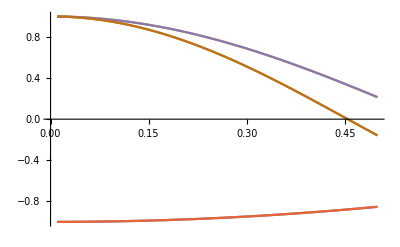

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True]
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={1.04,2.7,3.4};
ωrl={0.6,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
dt=0.01;
t=50.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0].ψt;
ψct=X1.ψ000;
ψct=ψct;
For[ti=dt,ti≤t,ti+=dt,
ψt=Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];
];
```

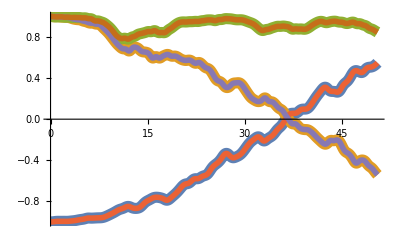

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

```mathematica
Ha[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];

h1=1/2(ω1-ωr1) Z1+Ω1 1/2(I0[3]+Cos[2 t ωr1+2ϕ1]I0[3]+ⅈ Cos[ωr1 t +ϕ1]Sin[t ωr1+ϕ1]Z1).X1;
h2=1/2(ω2-ωr2) Z2+Ω2 1/2(I0[3]+Cos[2 t ωr2+2ϕ2]I0[3]+ⅈ Cos[ωr2 t +ϕ2]Sin[t ωr2+ϕ2]Z2).X2;
h3=1/2(ω3-ωr3) Z3+Ω3 1/2(I0[3]+Cos[2 t ωr3+2ϕ3]I0[3]+ⅈ Cos[ωr3 t +ϕ3]Sin[t ωr3+ϕ3]Z3).X3 ;
h12=1/2 ω12 ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2);
h23=1/2 ω23 ( Cos[t ωr2+ϕ2]X2- Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3-Sin[t ωr3+ϕ3]Y3);
h31=1/2 ω31 ( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3).( Cos[t ωr1+ϕ1]X1-Sin[t ωr1+ϕ1]Y1);
h123=Λ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3);

htp = h1+h2+h3+h12+h23+h31+h123;

htp
];
```

```mathematica
Ua[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Ha[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={1.04,1.04,1.04};
ωrl={6.6,6.6,13.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
dt=0.01;
t=20.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0].ψt;
ψct=X1.ψ000;
ψct=ψct;
For[ti=dt,ti≤t,ti+=dt,
ψt=Ua[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];
];
```

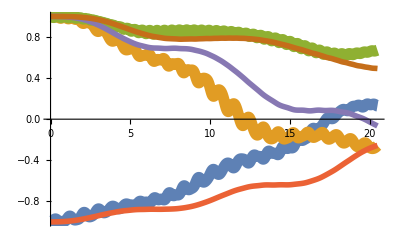

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={1.04,1.04,1.04};
ωrl={6.6,6.6,13.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
dt=0.01;
ψt = ψT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
ψat = ψaT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
ψt-ψat
```

{-0.0000526929-0.000104605 ⅈ,-0.00540366+0.00197409 ⅈ,-0.00819564+0.00230958 ⅈ,0.000707881-0.00324142 ⅈ,0.00162663+0.000107091 ⅈ,0.00166742+0.000201385 ⅈ,0.0036588+2.29783×10^-6 ⅈ,0.000728435+0.00136844 ⅈ}

```mathematica
dt=0.01;
t=20.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψt;
ψt=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψt;
ψat=X1.ψ000;
ψat=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψat;
For[ti=dt,ti≤t,ti+=dt,
ψt=U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψot;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψat=Ua[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψat;
ψaot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψat;

zc1=Conjugate[ψaot].Z1.ψaot;
zc2=Conjugate[ψaot].Z2.ψaot;
zc3=Conjugate[ψaot].Z3.ψaot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];
];
```

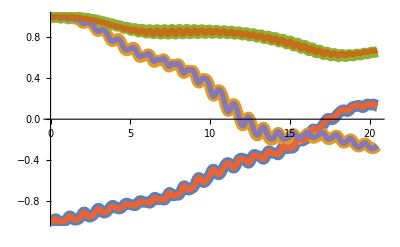

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

```mathematica
dt=0.01;
t=20.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψt;
ψt=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψt;
ψct=X1.ψ000;
For[ti=dt,ti≤t,ti+=dt,
ψt=U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψot;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];
];
```

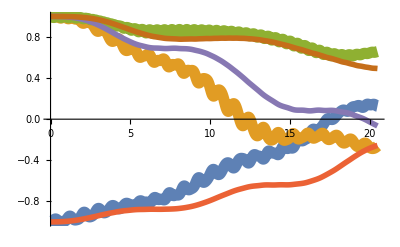

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

```mathematica
dt=0.01;
t=200.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
For[ti=dt,ti≤t,ti+=dt,
ψt=U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=ψt;


z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];


];
```

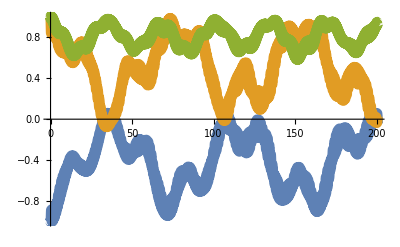

```mathematica
ListPlot[{z1l,z2l,z3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```